# Data Science and Machine Learning

## Lab session 04: Exploratory Data Analysis and Visualization

In this notebook, we will explore how to visualize data using a dataset obtained from the Global Preferences Survey, a globally representative dataset on risk and time preferences, positive and negative reciprocity, altruism, and trust.

## Data acquisition

Let's first import the (cleaned) data as a Dataset:

```mathematica
dataRaw = Import["MGT-492/Week_04/global_preference_survey.dta", "Dataset", HeaderLines -> 1];
```

It is best to not display large dataset. Instead you can for instance display the First row or a RandomSample of the data:

```mathematica
rand = RandomSample[dataRaw, 3]
```

The dataset contains 7 columns:
    	iso3 			Countries ISO3 code
    	patience 		Measure of time preference, i.e. how much future is valued compared to present
    	risktaking 		Measure of willingness to take risk
    	posrecip 		Positive reciprocity - Measure of propensity to act in a positively reciprocal way
    	negrecip 		Negative reciprocity - Measure of propensity to act in a negatively reciprocal way 
    	altruism 		Measure of propensity to donate
    	trust 			Measure of how trust in others

We can check the dimensions of our dataset:

```mathematica
{nobs,ncol}=Dimensions[dataRaw]
```

{76,7}

We have 76 observations, i.e. countries. 
Let's extract a list of these countries:

```mathematica
lisCountryISO3 = Normal @ dataRaw[All,"iso3"]
```

{AFG,DZA,ARG,AUS,AUT,BGD,BOL,BIH,BWA,BRA,KHM,CMR,CAN,CHL,CHN,COL,CRI,HRV,CZE,EGY,EST,FIN,FRA,GEO,DEU,GHA,GRC,GTM,HTI,HUN,IND,IDN,IRN,IRQ,ISR,ITA,JPN,JOR,KAZ,KEN,LTU,MWI,MEX,MDA,MAR,NLD,NIC,NGA,PAK,PER,PHL,POL,PRT,ROU,RUS,RWA,SAU,SRB,ZAF,KOR,ESP,LKA,SUR,SWE,CHE,TZA,THA,TUR,UGA,UKR,ARE,GBR,USA,VEN,VNM,ZWE}

Note: Normal converts an expression to a normal form. For a dataset, it will convert it to a mix of lists and associations.

Let's create a list of entities with our country (so far expressed with ISO3 code). The Interpreter allows to interpret an expression. If we specify "Country", it will recognize that each ISO3 code corresponds to a given country, and it will return the associated country identity. 
Recall that "/@" corresponds to Map

```mathematica
Interpreter["Country"]["CHE"]
```

Switzerland

```mathematica
countryEntities = Interpreter["Country"][#] & /@ lisCountryISO3
```

{Afghanistan,Algeria,Argentina,Australia,Austria,Bangladesh,Bolivia,Bosnia and Herzegovina,Botswana,Brazil,Cambodia,Cameroon,Canada,Chile,China,Colombia,Costa Rica,Croatia,Czech Republic,Egypt,Estonia,Finland,France,Georgia,Germany,Ghana,Greece,Guatemala,Haiti,Hungary,India,Indonesia,Iran,Iraq,Israel,Italy,Japan,Jordan,Kazakhstan,Kenya,Lithuania,Malawi,Mexico,Moldova,Morocco,Netherlands,Nicaragua,Nigeria,Pakistan,Peru,Philippines,Poland,Portugal,Romania,Russia,Rwanda,Saudi Arabia,Serbia,South Africa,South Korea,Spain,Sri Lanka,Suriname,Sweden,Switzerland,Tanzania,Thailand,Turkey,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,Venezuela,Vietnam,Zimbabwe}

We can add our list of entities to our dataset, which will allow not only an easier access to our data, but also to access all the country properties available in WL (e.g. GDP, population, etc.)

To do so, we can Join two associations:
	- one that associates the key "country" to the list of country entities,
	- one that associates each of the column of our dataset and the associated values for each country.
 The Normal form our dataset is a list of associations, each country is an association:  
 	{...,<|"iso3"→"UKR" ,  "patience"→-0.181666, "risktaking"→-0.218668, "posrecip"→0.165837, "negrecip"→-0.19131, "altruism"→-0.122266, "trust"→-0.092387|>, ...} 
 We use Transpose to transform the dataset into an association of lists (and reciprocally): 
            <|"iso3"→{...,"UKR",...} ,  "patience"→{...,-0.181666,...}, ...|>
  Once the two association of lists joined, we convert the result into a dataset, and transpose again into a list of associations.

```mathematica
data = Transpose @Dataset @Join[<|"country"->countryEntities |> , Normal @ Transpose @ dataRaw];
```

```mathematica
First[data]
First[data]["country"]
First[data]["country"]["Population"]
```

Afghanistan

38928341 people

## Descriptive statistics

Let's first create a list of our features (patience, risktaking, posrecip, negrecip, altruism, trust).
To do so, we first drop the columns "iso3" and "country" using KeyDrop.
Then, we extract the Keys  of our dataset.

```mathematica
keyList = Normal @ KeyDrop[Transpose @data,{"iso3", "country"}][Keys]
```

{patience,risktaking,posrecip,negrecip,altruism,trust}

Note that we transposed the dataset. If we did not, the result would be a list of 76 lists (one for each row of the dataset) each containing {patience, risktaking, posrecip, negrecip, altruism, trust}. Hence, instead of transposing the dataset, another option would be to extract for instance the first list of this nested list.

A good way to start exploring our dataset is to do a BoxWhiskerChart:

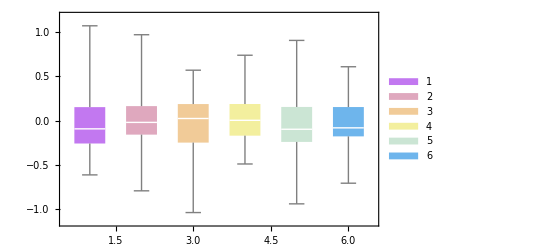

```mathematica
BoxWhiskerChart[Normal@data[All,#]& /@keyList, 
                                                      ChartLegends ->keyList, 
                     ChartStyle->"Pastel"]
```

A box plot allows to visualize if there are potential outliers: the minimum and/or maximum could be "absurd".

Note that you can visualize the Min, Max, Median, 25% and 75% Quantile directly by mousing over the graph!
You can also compute them:

```mathematica
data[All,"patience"][Min]
data[All,"patience"][Median]
data[All,"patience"][Max]
Quantile[data[All,"patience"],{0,0.25,0.5,0.75,1}]
```

-0.61252

-0.0925161

1.07145

Let's visualize the quantile info with a dataset. To do so, we can use AssociationThread to create an association between the keys {"Min","25%", "Median", "75%", "Max"} and a list of the quantiles, and convert this association into a dataset.

```mathematica
statPatience = Dataset@ AssociationThread[{"Min","25%", "Median", "75%", "Max"}, Normal @ Quantile[data[All,"patience"],{0,0.25,0.5,0.75,1}]]
```

We can compute the Correlation matrix, and display it as a matrix. 
Values allows to extract the values of an association (removing the keys):

```mathematica
corr =Correlation[Normal @data[All,keyList][Values]];
MatrixForm[corr]
```

(1. | 0.230358 | 0.0155394 | 0.258087 | -0.010385 | 0.189909
0.230358 | 1. | -0.256096 | 0.192764 | -0.0151752 | -0.0614531
0.0155394 | -0.256096 | 1. | -0.153624 | 0.711019 | 0.363077
0.258087 | 0.192764 | -0.153624 | 1. | -0.131952 | 0.15989
-0.010385 | -0.0151752 | 0.711019 | -0.131952 | 1. | 0.272735
0.189909 | -0.0614531 | 0.363077 | 0.15989 | 0.272735 | 1.)

To help visualize our correlation matrix, we can convert it to a dataset. Since we want to label both rows and columns, we need to repeat the Dataset and AssociationThread operations.

```mathematica
Dataset @ AssociationThread[keyList, Normal @ Transpose @Dataset @AssociationThread[keyList,corr]]
```

## Visualization

The Wolfram Language provides many Data Visualization functions. Let's explore some of them!

### Standard Plot

ListPlot allows to design scatter plot:

```mathematica
ListPlot[Transpose @Normal@{data[All,"posrecip"],data[All,"altruism"]},
                                                       PlotMarkers ->"OpenMarkers",
                      PlotLabel -> Style[Framed["Altruism and positive reciprocity"], White, Background -> Lighter[Blue]],
                                         AxesLabel -> {"Positive reciprocity","Altruism"}]
```

-Graphics-

### Information visualization

Documentation: Charting and Information visualization

#### Bar Chart

Let's represent the GDP per capita of a subset of our sample using a BarChart:

```mathematica
randData = RandomSample[data, 10];
```

We start by constructing a (reverse-)sorted association between our country entities and their GDP per capita.

```mathematica
gdpCapitaRand = randData[#, "country"]["GDP"]/randData[#, "country"]["Population"]&/@ Range[Length[randData] ];
randCountryLis = Normal @ randData[All, "country"];
assoCountryGDPCapita = ReverseSort @ AssociationThread[randCountryLis,gdpCapitaRand ]
```

<|Switzerland→81237.8 $,United States→64665.2 $,Germany→46084.3 $,United Kingdom→41674.4 $,Lithuania→20066.7 $,Bolivia→3503.4 $,Morocco→3242.98 $,Moldova→2966.99 $,Zimbabwe→1442.57 $,Tanzania→1057.64 $|>

We then use this association to build our bar chart:

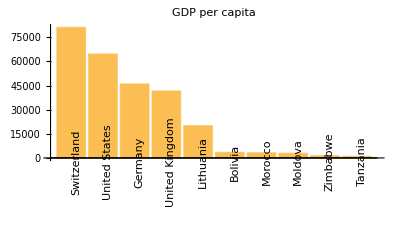

```mathematica
BarChart[assoCountryGDPCapita,
                        ChartLabels ->Placed[Keys[assoCountryGDPCapita],Below, Rotate[#, Pi/2] &],
          PlotLabel -> Style["GDP per capita",Blue]]
```

#### Pie Chart

Let's do a PieChart of the population of our countries:

```mathematica
popRand =randData[#, "country"]["Population"]&/@ Range[Length[randData] ];
assoCountryPop = AssociationThread[randCountryLis,popRand ];
sharePop = Round[#*100/Total[#],0.1]&[assoCountryPop];
```

```mathematica
PieChart[assoCountryPop,
                 PlotLabel -> Style["Population",Blue],
                 ChartStyle -> "DarkRainbow",
                 ChartLabels -> Quantity[Values[sharePop],"%"],
                 ChartLegends ->Keys[assoCountryPop]]
```

-Graphics-

### Statistical visualization

Documentation: Statistical Visualization

We have seen before a BoxWhiskerChart.

We will now do a Histogram of the risktaking feature:

```mathematica
Histogram[data[All,"risktaking"],
                                  ChartElementFunction -> "FadingRectangle",
             ChartStyle -> Orange]
```

-Graphics-

Show allows to combine several graphics. 
Let's see how our data compares to a Truncated NormalDistribution using a Plot.

First, we can create our histogram. The "Probability" option allows to normalize the counting:

```mathematica
dataRisk = Normal @data[All,"risktaking"];
histRisk = Histogram[dataRisk,Automatic, "Probability"];
```

Then, let's design the plot our normal distribution:

```mathematica
minRisk = Min @ dataRisk;
maxRisk = Max @ dataRisk;
muRisk = Median @ dataRisk;
sigmaRisk = StandardDeviation @ dataRisk;
normalDis = NormalDistribution[muRisk, sigmaRisk];
normalDisPlot =  Plot[PDF[normalDis, x]*0.25, {x,minRisk, maxRisk}, PlotStyle -> Red];
```

Finally, we can combine our two plots (I multiplied the normal distribution by 0.25 for a better visualization):

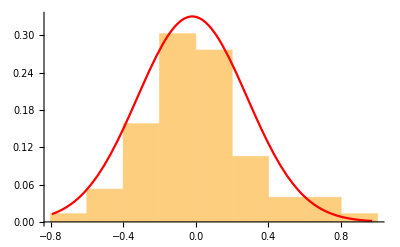

```mathematica
Show[histRisk, normalDisPlot]
```

### Time Visualization

Documentation: Time visualization

Let's plot the evolution of unemployment rate for a few countries using DateListPlot:

```mathematica
unemployment =EntityValue[randData[#, "country"],
                         EntityProperty["Country","UnemploymentRate",{"Date" -> All} ]]&/@ Range[Length[randData] ];
assoCountryUnemployment = AssociationThread[randCountryLis,unemployment ];
```

```mathematica
DateListPlot[assoCountryUnemployment, PlotLabel -> "Evolution of unemployment rate"]
```

-Graphics-

### Geographic Visualization

There exists plenty of Geographic Visualization options, such as GeoRegionValuePlot:

```mathematica
geoAltruism = AssociationThread[Normal @ data[All,"country"], Normal @data[All,"altruism"]];
```

```mathematica
GeoRegionValuePlot[geoAltruism, ColorFunction -> "TemperatureMap"]
```

-Graphics-

A geographic plot is a great way to visualize the missing countries (regions) in your sample!

### Grid of graphs

We can visualize a Grid of graphics using Table:

```mathematica
plotPreference[i_,j_]:=ListPlot[Transpose @Normal@{data[All,i],data[All,j]}, AxesLabel -> {i,j}];
Grid[Table[plotPreference[i,j],{i,keyList},{j,keyList}], Frame -> All]
```

-Graphics-

### Dynamic Visualization

We can also design dynamic visualization using for instance Manipulate

```mathematica
Manipulate[plotPreference[i,j],{i,keyList},{j,keyList}]
```

```mathematica
Manipulate[Histogram[data[All,pref]],{pref,keyList}]
```

## Data operations

### Counting

You can Count the number of elements that match a given pattern.

For instance, if we want to count the number of countries with a positive altruism value:

```mathematica
Count[data[All,"altruism"], u_ /;( u>0)]
```

30

Note: "/;" is a Condition, it allows to test a pattern, here we test the values "u" (each country altruism value) that are positive "u>0".

You can also Counts the number of distinct elements of a column. It returns an association with the keys being each distinct element, and the value being the number of times that element appears.

### Selection

You can Select a subset of your dataset based on a given criteria. 
Select > Median
Select altruism >0 and ... <0
Select European countries

For instance, let's select the countries that have a positive patience and negative risk taking.
Recall that "#patience" is the short version of #["patience"], which allows to evaluate the values of the column "patience.

Note:
	&&	stands for the logical operator And
    	||	stands for the logical operator Or
        	==	stands for Equal
              !=	stands for Unequal

```mathematica
data[Select[#patience >0 &&#risktaking >0  &]]
```

Let's select the European countries:

```mathematica
euCountries =EntityList[ EntityClass["Country","Europe"]];
```

MemberQ allows to test whether an element belongs to a given list:

```mathematica
MemberQ[euCountries,data[#,"country"]] & /@Range[Length[countryEntities]]
```

{False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,True,False,True,True,True,False,True,False,True,False,False,True,False,False,False,False,False,True,False,False,False,False,True,False,False,True,False,True,False,False,False,False,False,True,True,True,False,False,False,True,False,False,True,False,False,True,True,False,False,False,False,True,False,True,False,False,False,False}

```mathematica
data[Select[MemberQ[euCountries, #country]&] ]
```

### Grouping

GroupBy allows to group elements.

Let's group our countries by continent.
We first add a column "continent" to our dataset:

```mathematica
contiCountry = data[#,"country"]["Continent"]& /@ Range[nobs];
```

```mathematica
dataConti = Transpose @Dataset @Join[<|"continent"->contiCountry |> , Normal @ Transpose @ data];
```

We can then group our countries by continent:

```mathematica
dataConti[GroupBy["continent"]]
```

## Useful Links

Numerical Operation on Data: statistics, distributions, and much more...

Data Visualization

Tutorial Patterns

Some literature on preferences:

Henrich, Joseph, et al. "In search of homo economicus: behavioral experiments in 15 small-scale societies." American Economic Review 91.2 (2001): 73-78. Link

Falk, Armin, et al. "Global evidence on economic preferences." The Quarterly Journal of Economics 133.4 (2018): 1645-1692. Link

Nowak, Martin A. "Five rules for the evolution of cooperation." science 314.5805 (2006): 1560-1563. Link

Fehr, Ernst, and Simon Gächter. "Reciprocity and economics: The economic implications of homo reciprocans." European economic review 42.3-5 (1998): 845-859. Link

[Advanced... but fascinating] Alger, Ingela, and Jörgen W. Weibull. "Homo moralis—preference evolution under incomplete information and assortative matching." Econometrica 81.6 (2013): 2269-2302. Link